```mathematica
SetDirectory["~/docs/research/commpatterns/data"]
```

/Users/vsvh/docs/research/commpatterns/data

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12}
```

{FontFamily→Latin Modern Roman,FontSize→12}

```mathematica
data = Import["contour.dat"]
```

```mathematica
points0 = Import["points0.dat"];
points1 = Import["points1.dat"];
points2 = Import["points2.dat"];
points3 = Import["points3.dat"]
```

{{1,0},{1,10},{1,20},{1,30},{1,40},{2,0},{2,10},{2,20},{2,30},{2,40},{2,50},{2,60},{3,0},{3,10},{3,20},{3,30},{3,40},{3,50},{3,60},{3,70},{3,80},{4,0},{4,10},{4,20},{4,30},{4,40},{4,50},{4,60},{4,70},{4,80},{4,90},{5,0},{5,10},{5,20},{5,30},{5,40},{5,50},{5,60},{5,70},{5,80},{5,90},{5,100},{5,110},{5,120},{5,130},{6,0},{6,10},{6,20},{6,30},{6,40},{6,50},{6,60},{6,70},{6,80},{6,90},{6,100},{6,110},{6,120},{7,0},{7,10},{7,20},{7,30},{7,40},{7,50},{7,60},{7,70},{7,80},{7,90},{7,100},{7,110},{8,0},{8,10},{8,20},{8,30},{8,40},{8,50},{8,60},{8,70},{8,80},{8,90},{8,100},{8,110},{9,0},{9,10},{9,20},{9,30},{9,40},{9,50},{10,0},{10,10},{10,20},{10,30},{10,40},{10,50},{10,60},{10,70},{10,80},{10,90},{10,100},{10,110},{11,0},{11,10},{11,20},{11,30},{11,40},{11,50},{11,60},{11,70},{11,80},{11,90},{11,100},{11,110},{11,120},{11,130},{11,140},{12,0},{12,10},{12,20},{12,30},{12,40},{12,50},{12,60},{12,70},{13,0},{13,10},{13,20},{13,30},{13,40},{13,50},{13,60},{13,70},{13,80},{13,90},{14,0},{14,10},{14,20},{14,30},{14,40},{14,50},{14,60},{14,70},{14,80},{14,90},{14,100},{14,110},{14,120},{14,130},{14,140},{15,0},{15,10},{15,20},{15,30},{15,40},{15,50},{15,60},{15,70},{15,80},{15,90},{15,100},{15,110},{15,120},{15,130},{15,140},{15,150},{15,160},{15,170},{16,0},{16,10},{16,20},{16,30},{16,40},{16,50},{16,60},{16,70},{16,80},{16,90},{16,100},{16,110},{17,0},{17,10},{17,20},{17,30},{17,40},{17,50},{17,60},{17,70},{17,80},{17,90},{17,100},{17,110},{17,120},{17,130},{18,0},{18,10},{18,20},{18,30},{18,40},{18,50},{18,60},{18,70},{18,80},{18,90},{18,100},{18,110},{18,120},{18,130},{19,0},{19,10},{19,20},{19,30},{19,40},{19,50},{19,60},{19,70},{19,80},{19,90},{19,100},{19,110},{19,120},{19,130},{19,140},{19,150},{19,160},{21,0},{21,10},{21,20},{21,30},{21,40},{21,50},{21,60},{21,70},{21,80},{21,90},{21,100},{21,110},{21,120},{21,130},{21,140},{22,0},{22,10},{22,20},{22,30},{22,40},{22,50},{22,60},{22,70},{22,80},{22,90},{22,100},{22,110},{22,120},{22,130},{22,140},{22,150},{22,160},{22,170},{25,0},{25,10},{25,20},{25,30},{25,40},{33,0},{33,10},{33,20},{33,30},{33,40},{33,50},{33,60},{33,70},{33,80},{33,90},{33,100},{33,110},{33,120},{33,130},{33,140},{33,150},{33,160}}

```mathematica
marker0 = Graphics[{EdgeForm[Thickness[0.2]],ColorData["RedBlueTones"][0], Disk[]}];
marker1 = Graphics[{EdgeForm[Thickness[0.2]],ColorData["RedBlueTones"][0.3], Disk[]}];
marker2 = Graphics[{EdgeForm[Thickness[0.2]],ColorData["RedBlueTones"][0.6], Disk[]}];
marker3 = Graphics[{EdgeForm[Thickness[0.2]],ColorData["RedBlueTones"][0.99], Disk[]}];
```

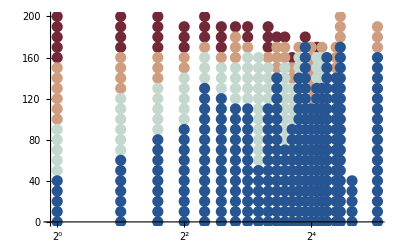

```mathematica
a = ListPlot[{points0, points1, points2, points3}, BaseStyle->texStyle, PlotMarkers->{{marker0, 0.02}, {marker1, 0.02}, {marker2, 0.02}, {marker3, 0.02}}, ScalingFunctions->{"Log2", None}]
```

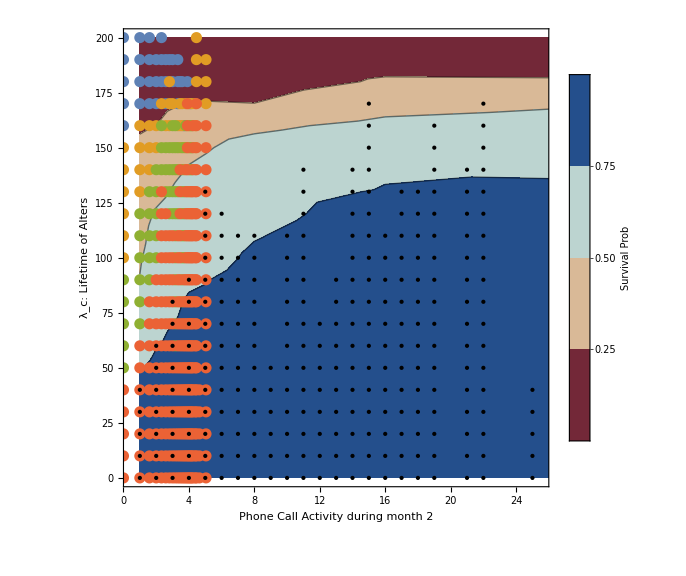

```mathematica
plot = Show[pc, a]
```

```mathematica
Export["../img/contour.pdf", plot]
```

../img/contour.pdf

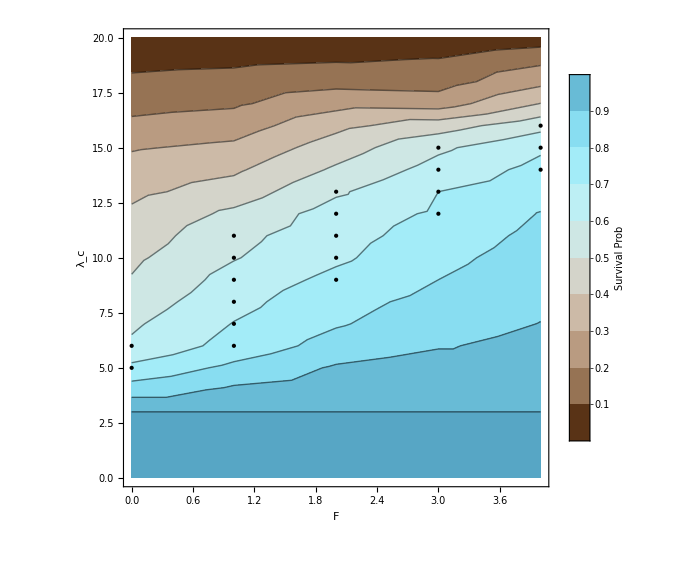

```mathematica
ListContourPlot[data,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Survival Prob",LabelStyle->{ Italic,FontFamily->"Helvetica", FontSize->20}],Right], FrameLabel->{"F","\[\Lambda]_c"}, LabelStyle->{FontFamily->"Helvetica", FontSize->18}, ImageSize->Large, ColorFunction->"BrownCyanTones", Epilog->{PointSize[Large],Black,Point[points3]}]
```

```mathematica
$FontFamilies
```

{Academy Engraved LET,Al Bayan,Alegreya SC,all-the-icons,Al Nile,Al Tarikh,American Typewriter,Andale Mono,Anonymous Pro for Powerline,Apple Braille,Apple Chancery,Apple Color Emoji,AppleGothic,AppleMyungjo,Apple SD Gothic Neo,Apple Symbols,Arial,Arial Black,Arial Hebrew,Arial Hebrew Scholar,Arial Narrow,Arial Rounded MT Bold,Arial Unicode MS,Arimo for Powerline,Avenir,Avenir Next,Avenir Next Condensed,Ayuthaya,Baghdad,Bangla MN,Bangla Sangam MN,Baskerville,Beirut,Big Caslon,Bitstream Vera Sans Mono,Bodoni 72,Bodoni 72 Oldstyle,Bodoni 72 Smallcaps,Bodoni Ornaments,Bradley Hand,Brush Script MT,Chalkboard,Chalkboard SE,Chalkduster,Charter,Clear Sans,Clear Sans Light,Clear Sans Medium,Clear Sans Thin,Cochin,Comic Sans MS,Copperplate,Corsiva Hebrew,Courier,Courier New,Cousine,Cousine for Powerline,Damascus,DecoType Naskh,DejaVu Sans Mono for Powerline,Devanagari MT,Devanagari Sangam MN,Didot,DIN Alternate,DIN Condensed,Diwan Kufi,Diwan Thuluth,Droid Sans Mono Dotted for Powerline,Droid Sans Mono for Powerline,Droid Sans Mono Slashed for Powerline,Droid Serif,EB Garamond,EB Garamond 12 All SC,EB Garamond SC,Economica,Euphemia UCAS,Farah,Farisi,Felipa,file-icons,Fira Mono for Powerline,Fira Sans,FontAwesome,Futura,Galvji,GB18030 Bitmap,Geeza Pro,Geneva,Gentium Basic,Georgia,Gill Sans,github-octicons,Go Mono for Powerline,Grantha Sangam MN,Gujarati MT,Gujarati Sangam MN,Gurmukhi MN,Gurmukhi MT,Gurmukhi Sangam MN,Hack,Hasklig,Hasklug Nerd Font,Heiti SC,Heiti TC,Helvetica,Helvetica Neue,Herculanum,Hiragino Maru Gothic ProN,Hiragino Mincho ProN,Hiragino Sans,Hiragino Sans GB,Hoefler Text,IBM 3270,IBM 3270 Narrow,IBM 3270 Semi-Narrow,Impact,InaiMathi,Inconsolata,Inconsolata-dz for Powerline,Inconsolata for Powerline,Inconsolata-g for Powerline,ITF Devanagari,ITF Devanagari Marathi,Kailasa,Kalam,Kannada MN,Kannada Sangam MN,Kefa,Khmer MN,Khmer Sangam MN,Kohinoor Bangla,Kohinoor Devanagari,Kohinoor Gujarati,Kohinoor Telugu,Kokonor,Krungthep,KufiStandardGK,Lao MN,Lao Sangam MN,Lato,League Gothic,Liberation Mono for Powerline,Lucida Grande,Luminari,Malayalam MN,Malayalam Sangam MN,Marker Felt,Material Icons,Menlo,Meslo LG L DZ for Powerline,Meslo LG L for Powerline,Meslo LG M DZ for Powerline,Meslo LG M for Powerline,Meslo LG S DZ for Powerline,Meslo LG S for Powerline,MesloLGS NF,Microsoft Sans Serif,Mishafi,Mishafi Gold,Monaco,monofur for Powerline,Mshtakan,Mukta Mahee,Muna,Myanmar MN,Myanmar Sangam MN,Nadeem,New Peninim MT,Noteworthy,Noto Mono for Powerline,Noto Nastaliq Urdu,Noto Sans Kannada,Noto Sans Myanmar,Noto Sans Oriya,Noto Serif Myanmar,NovaMono for Powerline,Optima,Oriya MN,Oriya Sangam MN,Osaka,Oswald,Palatino,Papyrus,Party LET,Phosphate,PingFang HK,PingFang SC,PingFang TC,Plantagenet Cherokee,Playfair Display,ProFont for Powerline,PT Mono,PT Sans,PT Sans Caption,PT Sans Narrow,PT Serif,PT Serif Caption,Raanana,Roboto,Roboto Condensed,Roboto Mono for Powerline,Roboto Mono Light for Powerline,Roboto Mono Medium for Powerline,Roboto Mono Thin for Powerline,Roboto Slab,Rockwell,Sana,Sathu,SauceCodePro Nerd Font,Savoye LET,Shadows Into Light Two,Shree Devanagari 714,SignPainter,Silom,Sinhala MN,Sinhala Sangam MN,Skia,Snell Roundhand,Songti SC,Songti TC,Source Code Pro,Source Code Pro for Powerline,Source Sans Pro,Source Serif Pro,Space Mono,Space Mono for Powerline,STIXGeneral,STIXIntegralsD,STIXIntegralsSm,STIXIntegralsUp,STIXIntegralsUpD,STIXIntegralsUpSm,STIXNonUnicode,STIXSizeFiveSym,STIXSizeFourSym,STIXSizeOneSym,STIXSizeThreeSym,STIXSizeTwoSym,STIXVariants,STSong,Sukhumvit Set,Symbol,Symbol Neu for Powerline,Tahoma,Tamil MN,Tamil Sangam MN,Telugu MN,Telugu Sangam MN,Thonburi,Times,Times New Roman,Tinos for Powerline,Titillium Web,Trattatello,Trebuchet MS,Twitter Color Emoji,Ubuntu Mono derivative Powerline,Verdana,Waseem,Weather Icons,Webdings,Wingdings,Wingdings 2,Wingdings 3,Yanone Kaffeesatz,Zapf Dingbats,Zapfino}

```mathematica
data2 = Import["contour2.dat"];
```

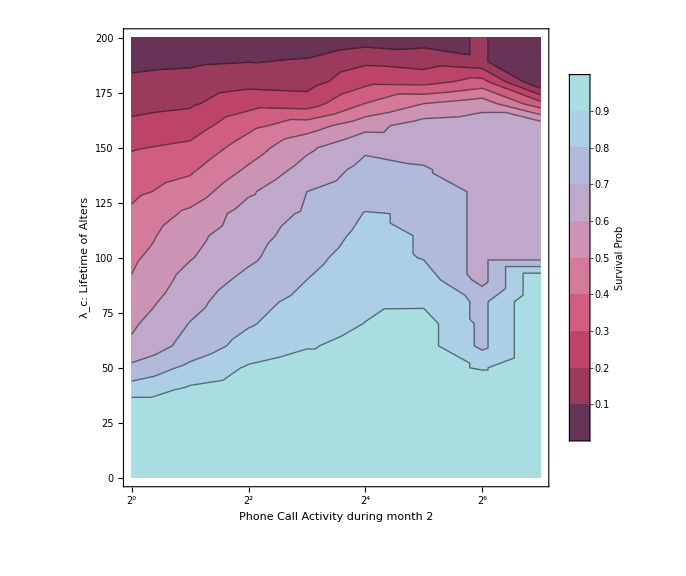

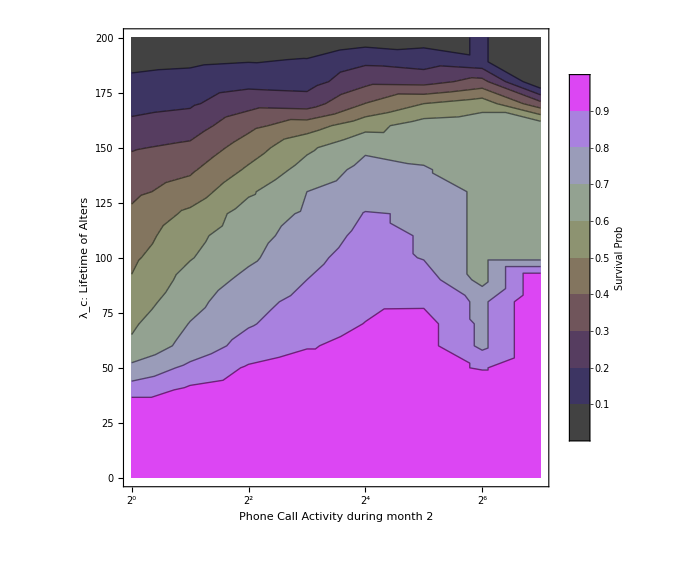

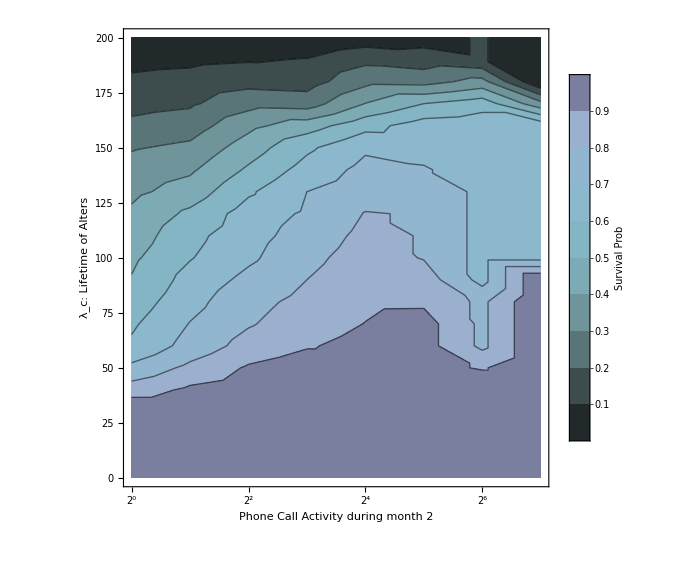

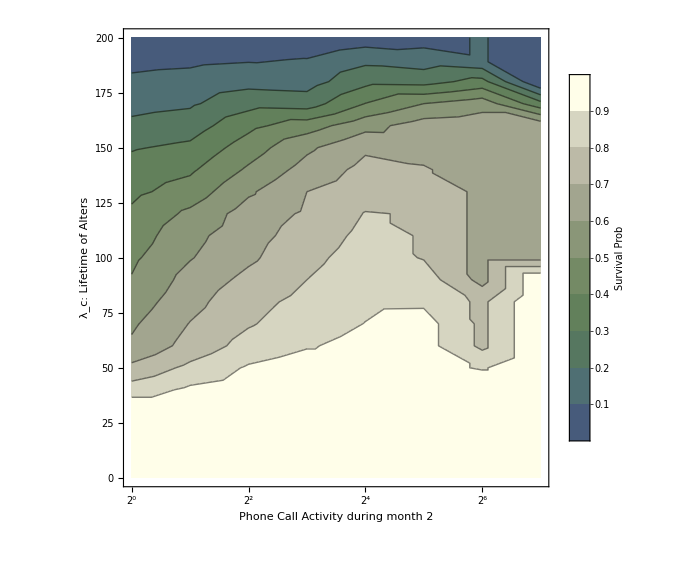

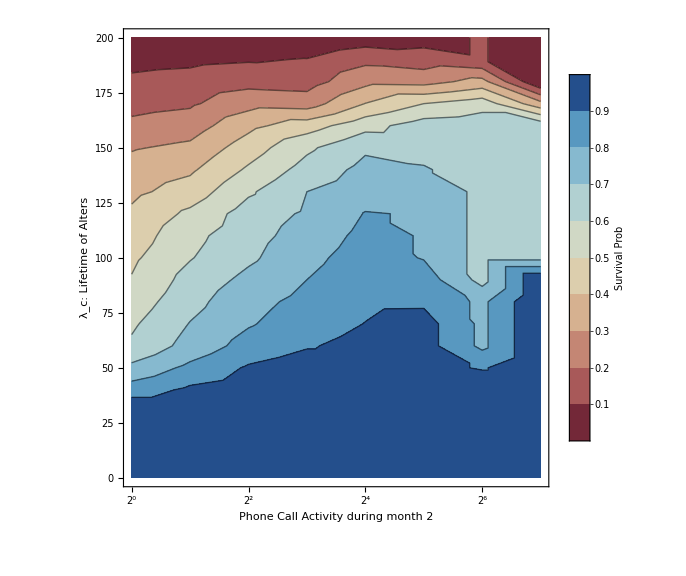

-Graphics-

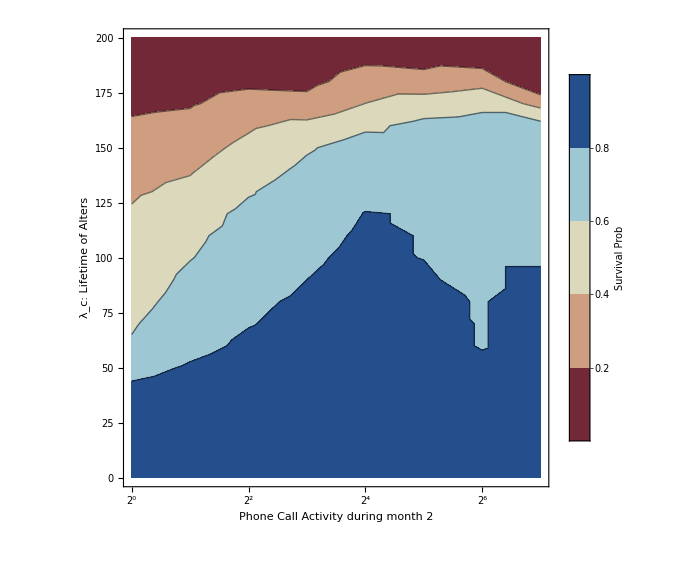

```mathematica
pc2 = ListContourPlot[data2,BaseStyle->texStyle, PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Survival Prob",LabelStyle->{ FontFamily->"Latin Modern Roman", FontSize->20}],Right], FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->18}, ImageSize->Large, ColorFunction->"CandyColors", Contours->9, ScalingFunctions->{"Log2", None}]
```

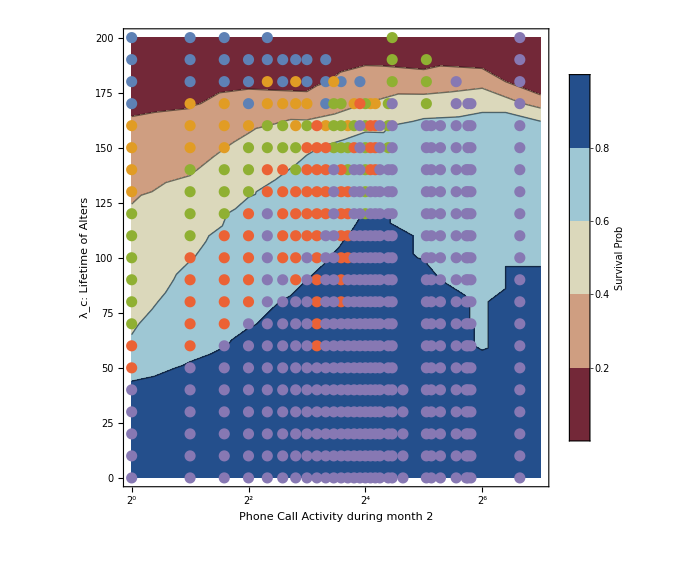

```mathematica
plot = Show[pc2, a]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
thebar = BarLegend[{"LightTemperatureMap",{0,1}},3, LegendLabel->"Survival Prob.", LabelStyle->{FontSize->12, FontFamily->"Latin Modern Roman"}, LegendFunction->Framed, LegendMarkerSize->500, LegendLayout->"Row"]
```

```mathematica
pp0 = ListPlot[points0,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}];
pp1 = ListPlot[points1,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}];
pp2 = ListPlot[points2,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}];
pp3 = ListPlot[points3,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}];
```

```mathematica
p11 = ListContourPlot[data,BaseStyle->texStyle, FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Medium, ColorFunction->"LightTemperatureMap", Contours->3, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}];
p12 = ListContourPlot[data,BaseStyle->texStyle, FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Medium, ColorFunction->"LightTemperatureMap", Contours->3, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}];
p21 = ListContourPlot[data,BaseStyle->texStyle, FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Medium, ColorFunction->"LightTemperatureMap", Contours->3, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}];
p22 = ListContourPlot[data,BaseStyle->texStyle,FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Medium, ColorFunction->"LightTemperatureMap", Contours->3, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}];
```

```mathematica
g11 = Show[p11, pp0];
g12 = Show[p12, pp1];
g21 = Show[p21, pp2];
g22 = Show[p22, pp3];
```

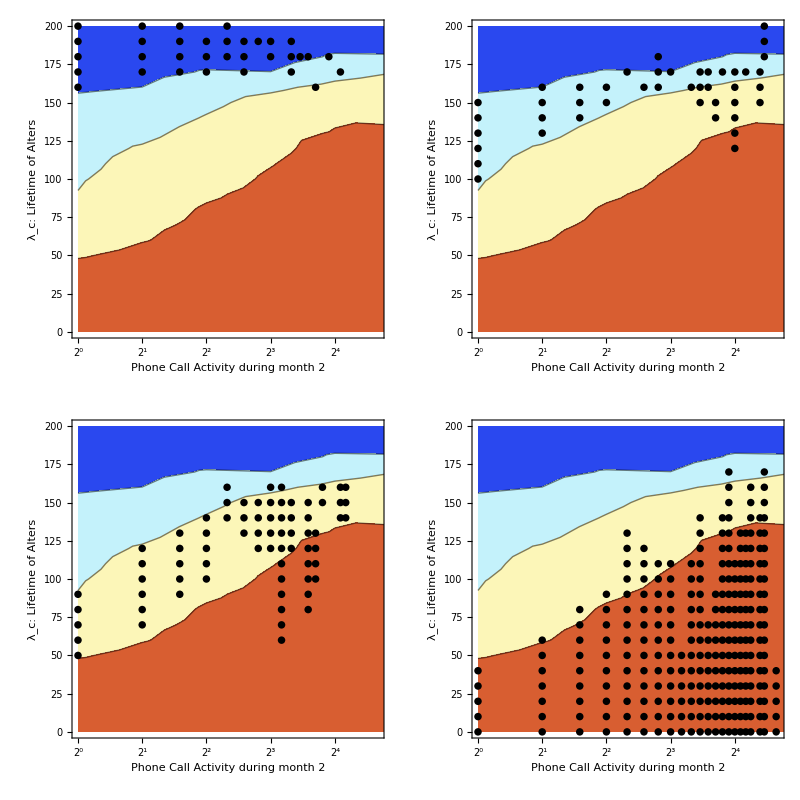

```mathematica
grid = GraphicsGrid[{{g11, g12}, {g21, g22}}, ImageSize->Full, Spacings->{0, 0}]
```

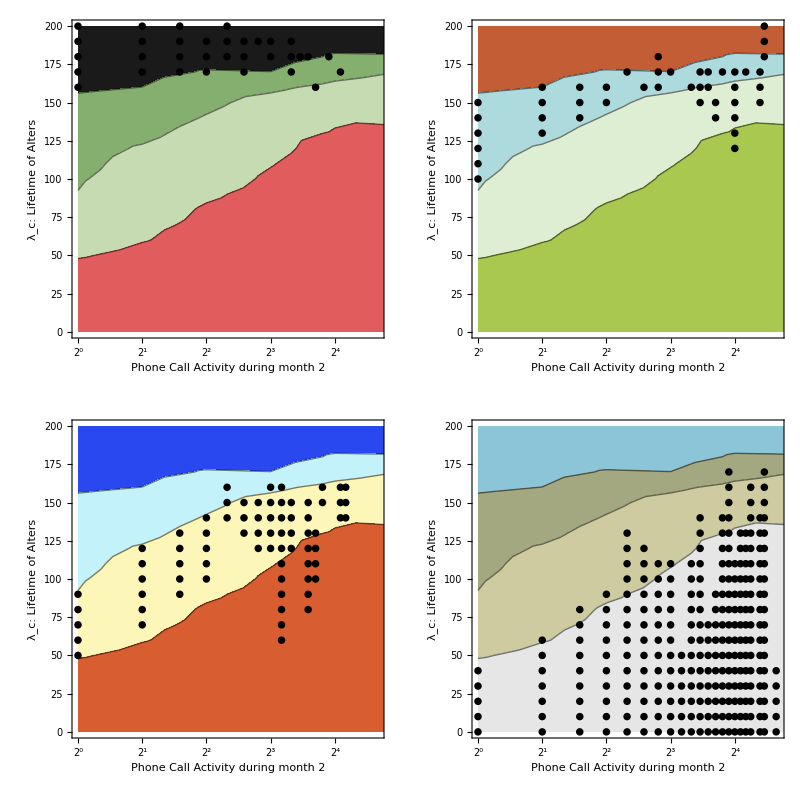

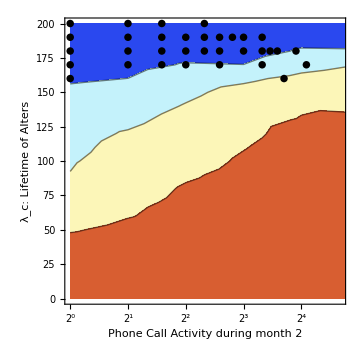
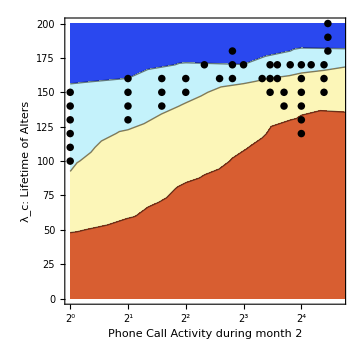
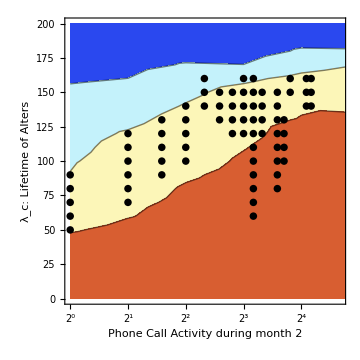
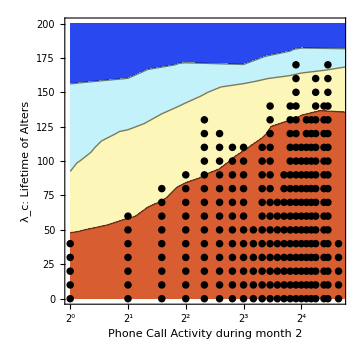
-Graphics- | -Graphics-
-Graphics- | -Graphics-
 |

```mathematica
Grid[{{g11, g12}, {g21,g22}, {thebar,SpanFromLeft}}]
```

```mathematica
Export["/home/vsvh/back/grid.pdf",%376,"PDF"]
```

/home/vsvh/back/grid.pdf

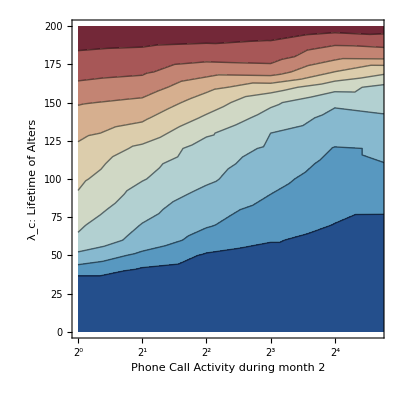

```mathematica
a = ListContourPlot[data,BaseStyle->texStyle,FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Automatic, ColorFunction->"RedBlueTones", Contours->9, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}]
```

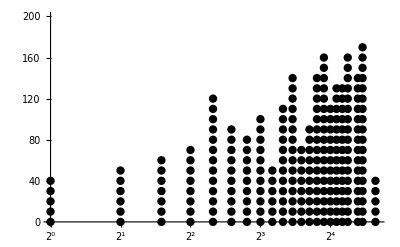

```mathematica
b = ListPlot[points4,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}]
```

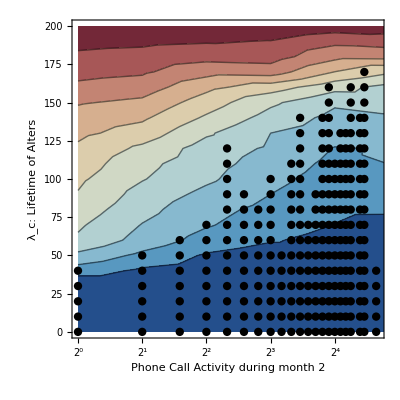

```mathematica
Show[a, b]
```